```mathematica
<<QINisq`
gghz[a_,b_]:={a,0,0,0,0,0,0,b};
gw[c_,d_,e_]:={0,c,d,0,e,0,0,0};
gsw[f_,g_,h_]:={0,0,0,f,0,g,h,0};
GME[ρ_,partitions_]:=√(2(1-Tr[MatrixPower[PartialTrace[ρ,{2,2,2},partitions],2]]));
τ3[ψ_]:=Module[{d1,d2,d3},
d1=ψ[[1]]^2 ψ[[8]]^2+ψ[[2]]^2 ψ[[7]]^2+ψ[[3]]^2 ψ[[6]]^2+ψ[[4]]^2 ψ[[5]]^2;
d2=ψ[[1]]ψ[[8]]ψ[[4]]ψ[[5]]+ψ[[1]]ψ[[8]]ψ[[3]]ψ[[6]]+ψ[[1]]ψ[[8]]ψ[[2]]ψ[[7]]+ψ[[4]]ψ[[5]]ψ[[3]]ψ[[6]]+ψ[[4]]ψ[[5]]ψ[[2]]ψ[[7]]+ψ[[3]]ψ[[6]]ψ[[2]]ψ[[7]];
d3=ψ[[1]]ψ[[7]]ψ[[6]]ψ[[4]]+ψ[[8]]ψ[[2]]ψ[[3]]ψ[[5]];
Return[4Abs[d1-2d2+4d3]];
];
indexToQubitIndices[n_,numQubits_]:=PadLeft[IntegerDigits[n-1,2],numQubits];
permutationMatrix[permutation_]:=With[{numQubits=Length@permutation},SparseArray[{{i_,j_}:>1/;Equal[Permute[indexToQubitIndices[i,numQubits],permutation],indexToQubitIndices[j,numQubits]]},2^numQubits {1,1}]];
M[i_]:=Switch[i,1,permutationMatrix[{4,2,3,1,5,6}],2,permutationMatrix[{1,5,3,4,2,6}],3,permutationMatrix[{1,2,6,4,5,3}]];
```

Package QI version 0.4.40 (last modification: 22/01/2023).

Package QIExtras 0.0.14 (last modification: 27/08/2023).

Package QINisq 0.0.13 (last modification: 18/10/2023).

## 1 Localized State

```mathematica
$Assumptions=0<=a<=1/(√2)∧0<ϕ<=2π∧0<=p<=1
ψ[p_,a_,ϕ_]:=√p gw[a,-√(1-2 a^2),a]+√(1-p) ⅇ^(ⅈ ϕ)gghz[1,0];
```

0≤a≤1/(√2)&&0<ϕ≤2 π&&0≤p≤1

```mathematica
Ψ=ψ[p,a,ϕ]
ρ=FullSimplify[Outer[Times,Ψ*,Ψ]]
eq1=FullSimplify[GME[ρ,{1,2}]]
eq2=FullSimplify[GME[ρ,{1,3}]]
```

{ⅇ^(ⅈ ϕ) √(1-p),a √p,-√(1-2 a^2) √p,0,a √p,0,0,0}

(1-p | a ⅇ^(-ⅈ ϕ) √((1-p) p) | -ⅇ^(-ⅈ ϕ) √((-1+2 a^2) (-1+p) p) | 0 | a ⅇ^(-ⅈ ϕ) √((1-p) p) | 0 | 0 | 0
a ⅇ^(ⅈ ϕ) √((1-p) p) | a^2 p | -a √(1-2 a^2) p | 0 | a^2 p | 0 | 0 | 0
-ⅇ^(ⅈ ϕ) √((-1+2 a^2) (-1+p) p) | -a √(1-2 a^2) p | p-2 a^2 p | 0 | -a √(1-2 a^2) p | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
a ⅇ^(ⅈ ϕ) √((1-p) p) | a^2 p | -a √(1-2 a^2) p | 0 | a^2 p | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

2 a √(1-a^2) p

2 a √(2-4 a^2) p

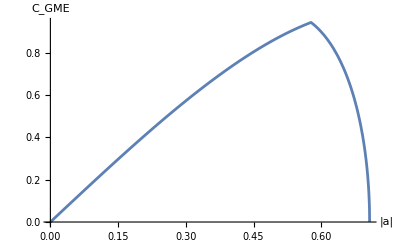

```mathematica
Plot[Min[{eq1,eq2}]/.p->1,{a,0,1/(√2)},AxesLabel->{"|a|",Subscript[C, GME]}]
```

## 2 Localized States

```mathematica
$Assumptions=0<=a<=1/(√2)∧0<=ϕ1<2π∧0<=ϕ2<2π∧0<=ϕ3<2π∧0<=p<=1∧0<=q<=1∧0<=r<=1∧0<=p+q+r<=1
ψ[p_,q_,r_,a_,ϕ1_,ϕ2_,ϕ3_]:=√p gw[a,-√(1-2 a^2),a]+√q ⅇ^(ⅈ ϕ1)gw[1/(√2),0,-1/(√2)]+√r ⅇ^(ⅈ ϕ2)gsw[√((1-2 a^2)/2),-(2a)/(√2),√((1-2 a^2)/2)]+√(1-p-q-r)ⅇ^(ⅈ ϕ3)gghz[1,0];
```

0≤a≤1/(√2)&&0≤ϕ1<2 π&&0≤ϕ2<2 π&&0≤ϕ3<2 π&&0≤p≤1&&0≤q≤1&&0≤r≤1&&0≤p+q+r≤1

```mathematica
Ψ=ψ[p,q,r,a,ϕ1,ϕ2,ϕ3]
ρ=FullSimplify[Outer[Times,Ψ*,Ψ]]
eq1=FullSimplify[(GME[ρ,{1,2}]/2)^2]/.{ϕ2->ϕ-ϕ3}//FullSimplify
eq2=FullSimplify[(GME[ρ,{1,3}]/2)^2]/.{ϕ2->ϕ-ϕ3}//FullSimplify
```

{ⅇ^(ⅈ ϕ3) √(1-p-q-r),a √p+(ⅇ^(ⅈ ϕ1) √q)/(√2),-√(1-2 a^2) √p,(√(1-2 a^2) ⅇ^(ⅈ ϕ2) √r)/(√2),a √p-(ⅇ^(ⅈ ϕ1) √q)/(√2),-√2 a ⅇ^(ⅈ ϕ2) √r,(√(1-2 a^2) ⅇ^(ⅈ ϕ2) √r)/(√2),0}

(1-p-q-r | ⅇ^(-ⅈ ϕ3) (a √p+(ⅇ^(ⅈ ϕ1) √q)/(√2)) √(1-p-q-r) | -ⅇ^(-ⅈ ϕ3) √((-1+2 a^2) p (-1+p+q+r)) | (ⅇ^(ⅈ (ϕ2-ϕ3)) √((-1+2 a^2) r (-1+p+q+r)))/(√2) | ⅇ^(-ⅈ ϕ3) (a √p-(ⅇ^(ⅈ ϕ1) √q)/(√2)) √(1-p-q-r) | -√2 a ⅇ^(ⅈ (ϕ2-ϕ3)) √(-r (-1+p+q+r)) | (ⅇ^(ⅈ (ϕ2-ϕ3)) √((-1+2 a^2) r (-1+p+q+r)))/(√2) | 0
ⅇ^(ⅈ ϕ3) (a √p+(ⅇ^(-ⅈ ϕ1) √q)/(√2)) √(1-p-q-r) | a^2 p+q/2+√2 a √(p q) Cos[ϕ1] | -√(p-2 a^2 p) (a √p+(ⅇ^(-ⅈ ϕ1) √q)/(√2)) | (ⅇ^(ⅈ ϕ2) (a √p+(ⅇ^(-ⅈ ϕ1) √q)/(√2)) √(r-2 a^2 r))/(√2) | a^2 p-q/2-ⅈ √2 a √(p q) Sin[ϕ1] | -a ⅇ^(-ⅈ (ϕ1-ϕ2)) (√2 a ⅇ^(ⅈ ϕ1) √p+√q) √r | (ⅇ^(ⅈ ϕ2) (a √p+(ⅇ^(-ⅈ ϕ1) √q)/(√2)) √(r-2 a^2 r))/(√2) | 0
-ⅇ^(ⅈ ϕ3) √((-1+2 a^2) p (-1+p+q+r)) | -1/2 √(p-2 a^2 p) (2 a √p+√2 ⅇ^(ⅈ ϕ1) √q) | p-2 a^2 p | ((-1+2 a^2) ⅇ^(ⅈ ϕ2) √(p r))/(√2) | 1/2 √(p-2 a^2 p) (-2 a √p+√2 ⅇ^(ⅈ ϕ1) √q) | √2 a ⅇ^(ⅈ ϕ2) √((1-2 a^2) p r) | ((-1+2 a^2) ⅇ^(ⅈ ϕ2) √(p r))/(√2) | 0
(ⅇ^(ⅈ (-ϕ2+ϕ3)) √((-1+2 a^2) r (-1+p+q+r)))/(√2) | 1/2 ⅇ^(-ⅈ ϕ2) (√2 a √p+ⅇ^(ⅈ ϕ1) √q) √(r-2 a^2 r) | ((-1+2 a^2) ⅇ^(-ⅈ ϕ2) √(p r))/(√2) | 1/2 (r-2 a^2 r) | 1/2 ⅇ^(-ⅈ ϕ2) (√2 a √p-ⅇ^(ⅈ ϕ1) √q) √(r-2 a^2 r) | -a √(1-2 a^2) r | 1/2 (r-2 a^2 r) | 0
ⅇ^(ⅈ ϕ3) (a √p-(ⅇ^(-ⅈ ϕ1) √q)/(√2)) √(1-p-q-r) | a^2 p-q/2+ⅈ √2 a √(p q) Sin[ϕ1] | √(p-2 a^2 p) (-a √p+(ⅇ^(-ⅈ ϕ1) √q)/(√2)) | (ⅇ^(ⅈ ϕ2) (a √p-(ⅇ^(-ⅈ ϕ1) √q)/(√2)) √(r-2 a^2 r))/(√2) | a^2 p+q/2-√2 a √(p q) Cos[ϕ1] | a ⅇ^(-ⅈ (ϕ1-ϕ2)) (-√2 a ⅇ^(ⅈ ϕ1) √(p r)+√(q r)) | (ⅇ^(ⅈ ϕ2) (a √p-(ⅇ^(-ⅈ ϕ1) √q)/(√2)) √(r-2 a^2 r))/(√2) | 0
-√2 a ⅇ^(-ⅈ (ϕ2-ϕ3)) √(-r (-1+p+q+r)) | -a ⅇ^(-ⅈ ϕ2) (√2 a √p+ⅇ^(ⅈ ϕ1) √q) √r | √2 a ⅇ^(-ⅈ ϕ2) √((1-2 a^2) p r) | -a √(1-2 a^2) r | a ⅇ^(-ⅈ ϕ2) (-√2 a √(p r)+ⅇ^(ⅈ ϕ1) √(q r)) | 2 a^2 r | -a √(1-2 a^2) r | 0
(ⅇ^(ⅈ (-ϕ2+ϕ3)) √((-1+2 a^2) r (-1+p+q+r)))/(√2) | 1/2 ⅇ^(-ⅈ ϕ2) (√2 a √p+ⅇ^(ⅈ ϕ1) √q) √(r-2 a^2 r) | ((-1+2 a^2) ⅇ^(-ⅈ ϕ2) √(p r))/(√2) | 1/2 (r-2 a^2 r) | 1/2 ⅇ^(-ⅈ ϕ2) (√2 a √p-ⅇ^(ⅈ ϕ1) √q) √(r-2 a^2 r) | -a √(1-2 a^2) r | 1/2 (r-2 a^2 r) | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

r/2-a^4 (p+r)^2+1/4 (q-r) (2 p+q+r)+a^2 (p^2-r (-1+2 q+r))+√2 a √(-r (-1+p+q+r)) (p Cos[ϕ]-q Cos[ϕ-2 ϕ1])+(1-2 a^2) √(-p q r (-1+p+q+r)) Cos[ϕ-ϕ1]-√2 a (-1+2 a^2) √(p q) (p+r) Cos[ϕ1]-2 a^2 p q Cos[ϕ1]^2

-((-1+2 a^2) (p q+r-p r-r^2+2 a^2 (p^2+p r+r^2)+2 √2 a p √(-r (-1+p+q+r)) Cos[ϕ]))

```mathematica
sol1=Reduce[eq1==0∧0<a<1/(√2)∧0<=ϕ1<2π∧0<=ϕ<2π∧0<=p<=1∧0<=q<=1∧0<=r<=1∧0<=p+q+r<=1,{p,q,r,ϕ1,ϕ},Reals]
```

$Aborted

```mathematica
sol2=Reduce[eq2==0∧0<a<1/(√2)∧0<=ϕ1<2π∧0<=ϕ<2π∧0<=p<=1∧0<=q<=1∧0<=r<=1∧0<=p+q+r<=1,{p,q,r,ϕ1,ϕ},Reals]
```

0<a<1/(√2)&&p==0&&0≤q≤1&&r==(-1+√(1/((-1+2 a^2)^2))-2 a^2 √(1/((-1+2 a^2)^2)))/(2 (-1+2 a^2))&&0≤ϕ1<2 π&&0≤ϕ<2 π

```mathematica
x=eq2/.{p->p,q->0,r->(1-p)/n,ϕ->π,a->0}//FullSimplify
Plot3D[x,{p,0,1},{n,1,10},AxesLabel->Automatic]
```

((-1+n) (-1+p)^2)/n^2

-Graphics3D-

## Other

```mathematica
Φ=((RZ[ϕ1].RY[θ1])⊗(RZ[ϕ2].RY[θ2])⊗(RZ[ϕ3].RY[θ3])⊗(RZ[ϕ4].RY[θ4])⊗(RZ[ϕ5].RY[θ5])⊗(RZ[ϕ6].RY[θ6]))[[All,1]];
σ=({{0, 0, 0, 0, 0, 0, 0, 0}, {0, 1/3, 1/3, 0, 1/3, 0, 0, 0}, {0, 1/3, 1/3, 0, 1/3, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 1/3, 1/3, 0, 1/3, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}});

ρ2=σ⊗σ;
II=Re[√(Φ*.ρ2.(M[1].M[2].M[3]).Φ)-Sum[√(Φ*.M[i]ᵀ.ρ2.M[i].Φ),{i,1,3}]];
NMaximize[II,{θ1,θ2,θ3,θ4,θ5,θ6,ϕ1,ϕ2,ϕ3,ϕ4,ϕ5,ϕ6},Method->"RandomSearch"]
```

{0.38025,{θ1→1.52999,θ2→1.53031,θ3→1.53046,θ4→-0.895663,θ5→0.89516,θ6→-0.894924,ϕ1→-0.469536,ϕ2→-0.469401,ϕ3→-0.46999,ϕ4→-0.469854,ϕ5→2.67147,ϕ6→-0.468947}}

```mathematica
σ=({{0, 0, 0, 0, 0, 0, 0, 0}, {0, 1/3, 1/3, 0, 1/3, 0, 0, 0}, {0, 1/3, 1/3, 0, 1/3, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 1/3, 1/3, 0, 1/3, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0}});
ρ2=σ⊗σ;

ψ[θ1_,θ2_,θ3_,ϕ1_,ϕ2_,ϕ3_]:=((RZ[ϕ1].RY[θ1])⊗(RZ[ϕ2].RY[θ2])⊗(RZ[ϕ3].RY[θ3])).UnitVector[8,1];
ψ2[θ1_,θ2_,θ3_,ϕ1_,ϕ2_,ϕ3_]:=ψ[θ1,θ2,θ3,ϕ1,ϕ2,ϕ3]⊗ψ[θ1,θ2,θ3,ϕ1,ϕ2,ϕ3];
Φ=.;
Φ[i_,j_,θ1_,θ2_,θ3_,θ4_,ϕ1_,ϕ2_,ϕ3_,ϕ4_]:=
(Switch[i,1,(RZ[ϕ4].RY[θ4])⊗id⊗id,2,id⊗(RZ[ϕ4].RY[θ4])⊗id,3,id⊗id⊗(RZ[ϕ4].RY[θ4])]⊗Switch[j,1,(RZ[ϕ4].RY[θ4])⊗id⊗id,2,id⊗(RZ[ϕ4].RY[θ4])⊗id,3,id⊗id⊗(RZ[ϕ4].RY[θ4])]).ψ2[θ1,θ2,θ3,ϕ1,ϕ2,ϕ3];
F[θ1_,θ2_,θ3_,θ4_,ϕ1_,ϕ2_,ϕ3_,ϕ4_]:=
Sum[If[i!=j,√(Φ[i,j,θ1,θ2,θ3,θ4,ϕ1,ϕ2,ϕ3,ϕ4]*.ρ2.(M[1].M[2].M[3]).Φ[i,j,θ1,θ2,θ3,θ4,ϕ1,ϕ2,ϕ3,ϕ4]),0],{i,1,3},{j,1,3}]-Sum[If[i!=j,√(Φ[i,j,θ1,θ2,θ3,θ4,ϕ1,ϕ2,ϕ3,ϕ4]*.M[i]†.ρ2.M[i].Φ[i,j,θ1,θ2,θ3,θ4,ϕ1,ϕ2,ϕ3,ϕ4]),0],{i,1,3},{j,1,3}]-Sum[√(Φ[i,i,θ1,θ2,θ3,θ4,ϕ1,ϕ2,ϕ3,ϕ4]*.M[i]†.ρ2.M[i].Φ[i,i,θ1,θ2,θ3,θ4,ϕ1,ϕ2,ϕ3,ϕ4]),{i,1,3}]
```

```mathematica
NMaximize[Re[F[θ1,θ2,θ3,θ4,ϕ1,ϕ2,ϕ3,ϕ4]],{θ1,θ2,θ3,θ4,ϕ1,ϕ2,ϕ3,ϕ4},Method->"RandomSearch"]
```

{1.,{θ1→-1.02275×10^-8,θ2→-8.41916×10^-9,θ3→2.08645×10^-8,θ4→-3.14159,ϕ1→1.18107,ϕ2→0.105139,ϕ3→1.19914,ϕ4→1.0594}}

```mathematica
0<=a<=1/(√2)∧0<=p<=1∧0<=q<=1∧0<=r<=1∧0<=p+q+r<=1∧θ∈Reals;
σ[p_,q_,r_,a_]:=p Outer[Times,gw[a,-√(1-2 a^2),a],gw[a,-√(1-2 a^2),a]]+q Outer[Times,gw[1/(√2),0,-1/(√2)],gw[1/(√2),0,-1/(√2)]]+r Outer[Times,gsw[√((1-2 a^2)/2),-(2a)/(√2),√((1-2 a^2)/2)],gsw[√((1-2 a^2)/2),-(2a)/(√2),√((1-2 a^2)/2)]]+√(1-p-q-r)Outer[Times,gghz[1,0],gghz[1,0]];
ρ2=σ[p,q,r,a]⊗σ[p,q,r,a];

ψ[θ1_,θ2_,θ3_,ϕ1_,ϕ2_,ϕ3_]:=((RZ[ϕ1].RY[θ1])⊗(RZ[ϕ2].RY[θ2])⊗(RZ[ϕ3].RY[θ3])).UnitVector[8,1];
ψ2[θ1_,θ2_,θ3_,ϕ1_,ϕ2_,ϕ3_]:=ψ[θ1,θ2,θ3,ϕ1,ϕ2,ϕ3]⊗ψ[θ1,θ2,θ3,ϕ1,ϕ2,ϕ3];
Φ[i_,j_,θ1_,θ2_,θ3_,θ4_,ϕ1_,ϕ2_,ϕ3_,ϕ4_]:=
(Switch[i,1,(RZ[ϕ4].RY[θ4])⊗id⊗id,2,id⊗(RZ[ϕ4].RY[θ4])⊗id,3,id⊗id⊗(RZ[ϕ4].RY[θ4])]⊗Switch[j,1,(RZ[ϕ4].RY[θ4])⊗id⊗id,2,id⊗(RZ[ϕ4].RY[θ4])⊗id,3,id⊗id⊗(RZ[ϕ4].RY[θ4])]).ψ2[θ1,θ2,θ3,ϕ1,ϕ2,ϕ3];
F[θ1_,θ2_,θ3_,θ4_,ϕ1_,ϕ2_,ϕ3_,ϕ4_]:=
Sum[If[i!=j,√(Φ[i,j,θ1,θ2,θ3,θ4,ϕ1,ϕ2,ϕ3,ϕ4]*.ρ2.(M[1].M[2].M[3]).Φ[i,j,θ1,θ2,θ3,θ4,ϕ1,ϕ2,ϕ3,ϕ4]),0],{i,1,3},{j,1,3}]-Sum[If[i!=j,√(Φ[i,j,θ1,θ2,θ3,θ4,ϕ1,ϕ2,ϕ3,ϕ4]*.M[i]†.ρ2.M[i].Φ[i,j,θ1,θ2,θ3,θ4,ϕ1,ϕ2,ϕ3,ϕ4]),0],{i,1,3},{j,1,3}]-Sum[√(Φ[i,i,θ1,θ2,θ3,θ4,ϕ1,ϕ2,ϕ3,ϕ4]*.M[i]†.ρ2.M[i].Φ[i,i,θ1,θ2,θ3,θ4,ϕ1,ϕ2,ϕ3,ϕ4]),{i,1,3}]

Simplify[F[0,0,0,0,0,0,0,0],0<=a<=1/(√2)∧0<=p<=1∧0<=q<=1∧0<=r<=1∧0<=p+q+r<=1∧_∈Reals]
```

-3 √(1-p-q-r)